RAKAVA OBOLENJA V SLOVENIJI IN SVETU

Analiza podatkov rakavih obolenj sveta ter analiza raka v Sloveniji.

## PRIDOBIVANJE PODATKOV:

Podatke o svetu sem pridobila iz WORLD CANCER REASRCH FUND INTERNATIONAL, ter podatke o Sloveniji iz ONKOLOŠKI INSTITUT SLOVENIJE, ter iz spletne strani SLORA.

## UVOD

Rakava obolenja predstavljajo eno največjih izzivov sodobne medicine in družbe kot celote. Rak je širok pojem, ki označuje skupino bolezni, pri katerih se celice v telesu nenadzorovano razmnožujejo in tvorijo tumorje. Vzroki za razvoj raka so pogosto kompleksniin jih ni mogoče povsem natančno določiti. Med dejavnike tevaganja nastanka raka spadajo kajenje, prekomerno uživanje alkohola, nezdrava prehrana, nezadostna telesba dejavnost itd.
Predstavila Vam bom podatke rakavih obolenj, naprimer koliko ljudi je bilo leta 2020 obolelih, katere vrste raka so zelo pogoste ter analizo podatkov o raku v Sloveniji skozi leta.

## RAKAVA OBOLENJA V SVETU:

Prvi graf je naraščajoča krivulja, ki predstavlja porast rakavih obolenj po vsem svetu skozi leta od 2000 do leta 2020. Podatki iz katerih je graf narejen predstavljajo stopnjo raka, glede na 100.000 prebivalcev.

```mathematica
prvaTabela= Import["C:\\Users\\Ula\\Desktop\\ROM\\svet po letih2.xlsx","Dataset",HeaderLines->1]//First
```

```mathematica
prvipodatki=prvaTabela//Values//Normal
```

{{2000.,286.},{2002.,300.},{2004.,319.},{2006.,319.},{2008.,335.},{2010.,347.},{2012.,341.},{2014.,337.},{2016.,358.},{2018.,359.},{2020.,358.}}

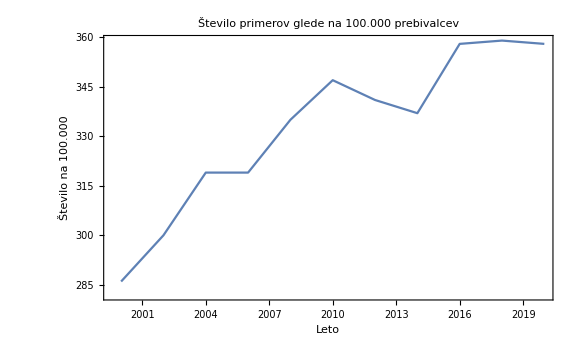

```mathematica
ListLinePlot[prvipodatki, PlotLabel->"Število primerov glede na 100.000 prebivalcev", FrameLabel->{"Leto", "Število na 100.000"}, Frame->{{True,False},{True,False}}]
```

Drugi graf je tortni diagram, ki predstavlja razdelitev po spolu za leto 2020. Kot kažeta tabela in diagram zboli statistično več moških kot žensk. Vendar pa je pomembno poudariti, da to ni enotna slika in obstajajo vrste raka, ki so pogostejše pri ženskah kot pri moških, ter obratno.

```mathematica
tabela1 = Import["C:\\Users\\Ula\\Desktop\\ROM\\spol2.xlsx","Dataset", HeaderLines->1]//First
```

```mathematica
podatki = tabela1//Values//Normal
```

{{moški,9.3×10^6},{ženske,8.8×10^6}}

```mathematica
podatki2 =podatki[[All,2]]//Normal
```

{9.3×10^6,8.8×10^6}

```mathematica
PieChart[podatki[[All,2]], ChartStyle->{Blue, Red},PlotLabel->"Število obolenj glede na spol",ChartLegends->{podatki[[All,1]]}, PlotRange->All, ImageSize->Medium]
```

-Graphics-

## VRSTE RAKAVIH OBOLENJ:

Obstaja veliko vrst raka, ki se med seboj razlikujejo po svojih značilnostih, simptomih, poteku bolezni in odzivu na zdravljenje. Vsaka vrsta raka ima svoje specifične značilnosti in lahko prizadane določene organe ali tkiva telesa.

Tretja skupina podtakov je predstavljena s stolpičnimi diagrami. Prvi diagram predstavlja nekaj zelo pogostih vrst rakavih obolenj, ki so skupne obema spoloma.

```mathematica
tabela3=Import["C:\\Users\\Ula\\Desktop\\ROM\\ŽE\\vrste raka\\vrste raka.xlsx","Dataset", "HeaderLines"->1]//First
```

```mathematica
podatki3 =tabela3//Values//Normal
```

{{Jetra,905.677},{Mehur,573.278},{Trebušna slinovka,495.773},{Ledvice,431.288},{Melanom,324.635},{Levkemija,474.519}}

```mathematica
pod3=podatki3[[All,2]]//Normal
```

{905.677,573.278,495.773,431.288,324.635,474.519}

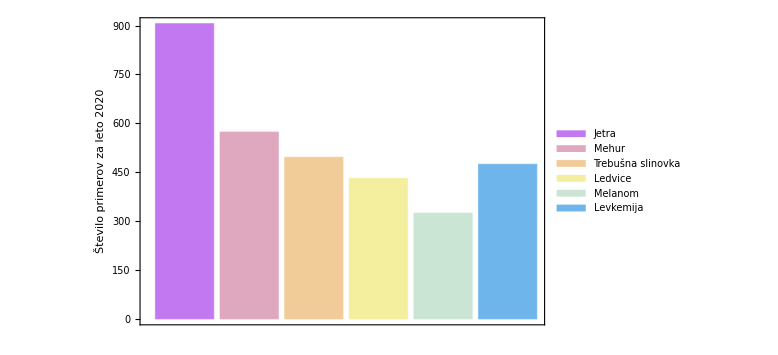

```mathematica
BarChart[pod3, ChartStyle->"Pastel",Frame->{{True,False},{True,False}},
ChartLegends->{podatki3[[All,1]]},FrameLabel->{None,"Število primerov za leto 2020"}, PlotRangePadding->{Automatic,{Scaled[0],Scaled[0.05]}}, ImageSize->Large]
```

Podatke za drugi in tretji diagram sem analizirala tako, da sem od vsakega spola vzela podatke za enake vrste rakavih obolenj. Iz njiju lahko razberemo, da je število primerov pri moških pri vsaki vrsti večje kot pri ženskah, saj moramo vedeti tudi, da statistično tudi znano, da je na svetu več moških. Opazi pa se pretirana razlika pri raku na trebuhu ter pri raku na jetrih, kjer je primerov pri moških izrazito veliko.

```mathematica
tabela4=Import["C:\\Users\\Ula\\Desktop\\ROM\\vrste raka na spol\\vrste raka glede na spol.xlsx", "Dataset", HeaderLines-> 1]//First
```

```mathematica
podatki4=tabela4//Values//Normal
```

{{Trebuh,719.523},{Jetra,632.32},{Mehur,440.864},{Levkemija,269.503},{Melanom,173.844},{Ledvica,271.249},{Možgani,168.346},{Trebušna slinovka,262.865}}

```mathematica
pod4=podatki4[[All,2]]//Normal
```

{719.523,632.32,440.864,269.503,173.844,271.249,168.346,262.865}

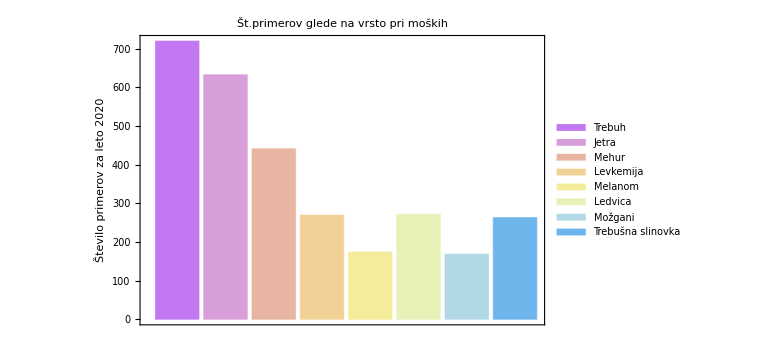

```mathematica
BarChart[pod4, ChartStyle->"Pastel",Frame->{{True,False},{True,False}},
ChartLegends->{podatki4[[All,1]]},PlotLabel->"Št.primerov glede na vrsto pri moških",FrameLabel->{None,"Število primerov za leto 2020"}, PlotRangePadding->{Automatic,{Scaled[0],Scaled[0.05]}}, ImageSize->Large]
```

```mathematica
tabela5=Import["C:\\Users\\Ula\\Desktop\\ROM\\vrste raka na spol\\vrste raka glede na spol2.xlsx", "Dataset", HeaderLines->1]//First
```

```mathematica
podatki5= tabela5//Values//Normal
```

{{Trebuh,269.58},{Jetra,273.357},{Mehur,132.414},{Levkemija,205.016},{Melanom,150.791},{Ledvica,160.039},{Možgani,139.756},{Trebušna slinovka,232.908}}

```mathematica
pod5=podatki5[[All,2]]//Normal
```

{269.58,273.357,132.414,205.016,150.791,160.039,139.756,232.908}

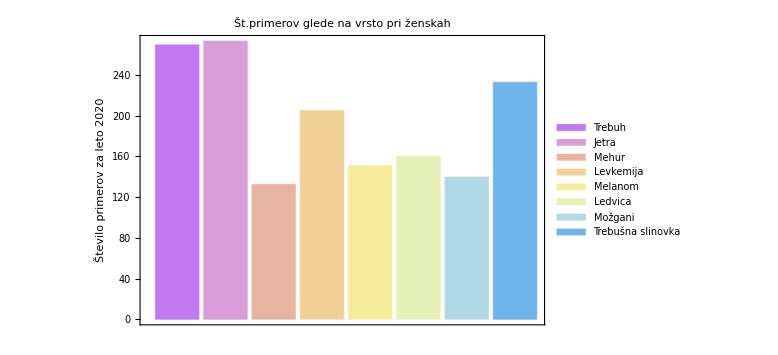

```mathematica
BarChart[pod5, ChartStyle->"Pastel",Frame->{{True,False},{True,False}},
ChartLegends->{podatki5[[All,1]]},FrameLabel->{None,"Število primerov za leto 2020"}, PlotLabel->"Št.primerov glede na vrsto pri ženskah",PlotRangePadding->{Automatic,{Scaled[0],Scaled[0.05]}}, ImageSize->Large]
```

## RAKAVA OBOLENJA V SLOVENIJI:

Rakava obolenja predstavljajo pomembno zdravstevno težavo tudi v Sloveniji. Slovenija je po vrsti v drugi deseterici po številu primerov rakavih obolenj.

Prvi podatki o raku v Sloveniji upodobljeni z stolpičnim diagramom predstavljajo število primerov po starosti za leto 2020.

```mathematica
tabela6 =Import["C:\\Users\\Ula\\Desktop\\ROM\\st.primerov po starosti slo\\št.primerov po starosti ter letih.xlsx", "Dataset", HeaderLines->1]//First
```

```mathematica
podatki6 = tabela6//Values//Normal
```

{{0-04,23.},{05-09,17.},{10-14,15.},{15-19,16.},{20-24,40.},{25-29,75.},{30-34,155.},{35-39,240.},{40-44,380.},{45-49,571.},{50-54,956.},{55-59,1347.},{60-64,2060.},{65-69,2633.},{70-74,2235.},{75-79,2300.},{80+,3291.}}

```mathematica
podatki7=podatki6[[All,2]]//Normal
```

{23.,17.,15.,16.,40.,75.,155.,240.,380.,571.,956.,1347.,2060.,2633.,2235.,2300.,3291.}

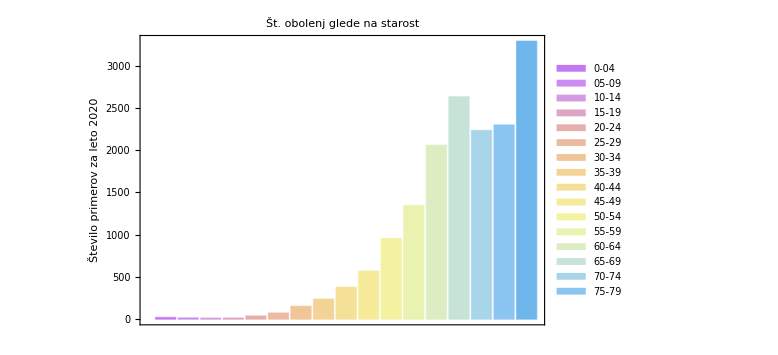

```mathematica
BarChart[podatki7, ChartStyle->"Pastel",Frame->{{True,False},{True,False}},
ChartLegends->{podatki6[[All,1]]},PlotLabel->"Št. obolenj glede na starost",FrameLabel->{None,"Število primerov za leto 2020"}, PlotRangePadding->{Automatic,{Scaled[0],Scaled[0.05]}}, ImageSize->Large]
```

Drugi podatki so upodobljeni z krivuljo in sicer predstavljajo število rakavih obolenj skozi leta, in sicer od leta 2000 do leta 2020.

```mathematica
tabela7 =Import["C:\\Users\\Ula\\Desktop\\ROM\\po letih.xlsx","Dataset", HeaderLines->1]//First
```

```mathematica
podatki8=tabela7//Values//Normal
```

{{2000.,9179.},{2002.,10045.},{2004.,11102.},{2006.,11524.},{2008.,12598.},{2010.,13572.},{2012.,13814.},{2014.,14249.},{2016.,15446.},{2018.,16270.},{2020.,16353.}}

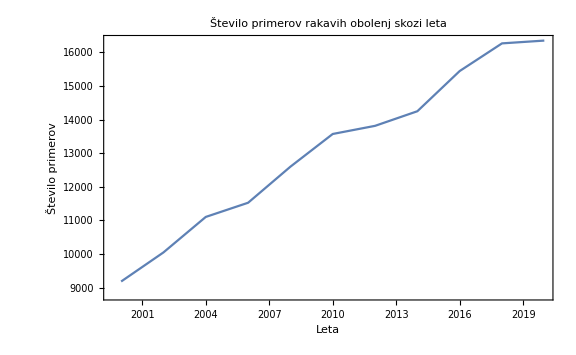

```mathematica
ListLinePlot[podatki8,PlotLabel->"Število primerov rakavih obolenj skozi leta",FrameLabel->{"Leta","Število primerov"}, Frame->{{True,False},{True,False}}, ImageSize->Large]
```

Tretji in zadnji stolpični diagram predstavlja podatke incidence, umrljivosti ter prevelence za leto 2020 v Sloveniji. Incidenca so novi primeri rakavih obolenj v letu 2020. Glede na prevelenco, ki pomeni, koliko je bilo aktivnih primerov oz. koliko ljudi je leta 2020 živelo oz. se zdravilo za rakom, je umrljivost po mojem mnjenju srednje visoka.

```mathematica
tabela8 =Import["C:\\Users\\Ula\\Desktop\\ROM\\podatki.xlsx","Dataset",HeaderLines->1]//First
```

```mathematica
podatki9=tabela8//Values//Normal
```

{{incidenca,16080.},{umrljivost,6285.},{prevelenca,121276.}}

```mathematica
podatki10=podatki9[[All,2]]
```

{16080.,6285.,121276.}

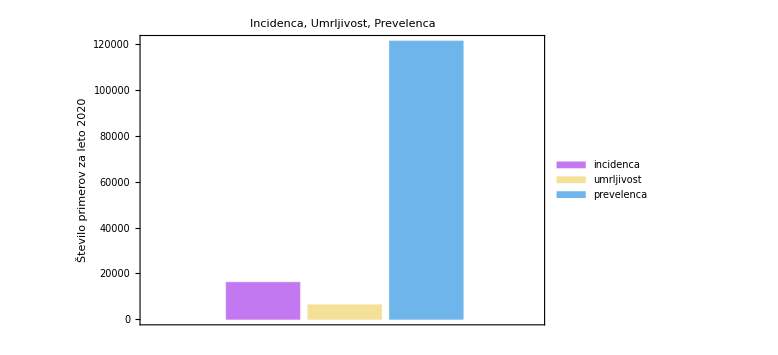

```mathematica
BarChart[podatki10, ChartStyle->"Pastel",Frame->{{True,False},{True,False}},
ChartLegends->{podatki9[[All,1]]},PlotLabel->"Incidenca, Umrljivost, Prevelenca",FrameLabel->{None,"Število primerov za leto 2020"}, PlotRangePadding->{Automatic,{Scaled[0],Scaled[0.05]}}, ImageSize->Large]
```